# Chiral potential V

## Using the elliptic functions to determine the chiral potentials

## The potential is constructed to depend on the modulus k explicitly

```mathematica
ClearAll["Global`*"]
```

Helper functions

```mathematica
thesispath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_,format_]:=Export[StringTemplate["``/``.``"][thesispath,name, format],object, ImageResolution->1500];
linspace[a_,b_,n_]:=Table[q,{q,a,b,(b-a)/(n-1)}];
```

Fit parameters

```mathematica
moisfit1={91,9,51};
moisfit2={13.53,101.76,52.94};
moisfit3={89,12,48};
spinvalues={22.5,18.5,14.5};
thetadegfit1=-119;
thetadegfit2=140;
thetadegfit3=-71;
oddspin=5.5;
magicpower=2;
A[k_,mois_]:=N[1/(2*#)&/@mois][[k]];
rad[theta_]:=N[theta*π/180];
j[k_,thetadeg_]:={oddspin*Cos[rad[thetadeg]],oddspin*Sin[rad[thetadeg]]}[[k]];
Afactor[spin_,thetadeg_,mois_]:=A[2,mois](1-j[2,thetadeg]/spin)-A[1,mois];
ufactor[spin_,thetadeg_,mois_]:=(A[3,mois]-A[1,mois])/Afactor[spin, thetadeg, mois];
v0factor[spin_,thetadeg_, mois_]:=-(A[1,mois]*j[1,thetadeg])/Afactor[spin,thetadeg,mois];
k[spin_,thetadeg_,mois_]:=√Abs[ufactor[spin,thetadeg,mois]];
period[k_]:=NIntegrate[1/(√(1-k^magicpower Sin[t]^2)),{t,0,π/2}];
```

Potential

The potential depends on the factors k=√(|u|) and v_0 explicitly

```mathematica
v0const[thetadeg_]:=v0factor[22.5,thetadeg,moisfit1];
uconst[thetadeg_]:=ufactor[22.5,thetadeg,moisfit1];
kconst[thetadeg_]:=k[22.5,thetadeg,moisfit1];
qvalues[k_]:=linspace[-4*period[k],4*period[k],200];
V[q_,spin_,k_,thetadeg_,magicpower_]:=(spin*(spin+1)*k^2+v0const[thetadeg]^2)*Sin[JacobiAmplitude[q,k^magicpower]]^2+(2*spin+1)*v0const[thetadeg]*Cos[JacobiAmplitude[q,k^magicpower]]*√(1-k^2*Sin[JacobiAmplitude[q,k^magicpower]]^2);
dvdq[p_,spin_,k_,thetadeg_,magicpower_]:=D[V[q,spin,k,thetadeg,magicpower],q]/.{q->p};
```

```mathematica
dvdq[-6.396969916238003,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]
```

-3.21186×10^-13

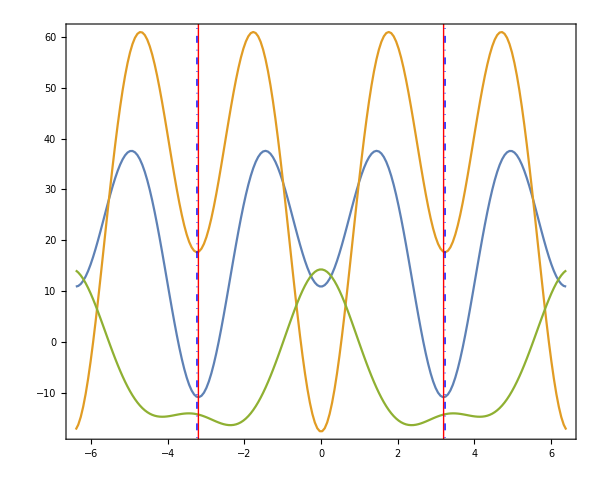

```mathematica
Show[ListLinePlot[{Table[{q,V[q,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]},{q,qvalues[kconst[thetadegfit1]]}],Table[{q,V[q,22.5,kconst[thetadegfit1+180],thetadegfit1+180,magicpower]},{q,qvalues[kconst[thetadegfit1]]}],Table[{q,0.5(V[q,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]-V[q,22.5,kconst[thetadegfit1+180],thetadegfit1+180,magicpower])},{q,qvalues[kconst[thetadegfit1]]}]},ImageSize->600,AspectRatio->0.8,Frame->True,Axes->True],Graphics[{Red,Thick,Line[{{-2*period[kconst[thetadegfit1]],-100},{-2*period[kconst[thetadegfit1]],100}}]}],Graphics[{Red,Thick,Line[{{2*period[kconst[thetadegfit1]],-100},{2*period[kconst[thetadegfit1]],100}}]}],Graphics[{Blue,DotDashed,Line[{{-2*period[kconst[thetadegfit1+180]],-100},{-2*period[kconst[thetadegfit1+180]],100}}]}],Graphics[{Blue,DotDashed,Line[{{2*period[kconst[thetadegfit1+180]],-100},{2*period[kconst[thetadegfit1+180]],100}}]}]]
```

```mathematica
qvalues[kconst[thetadegfit1]]
```

{-6.39697,-6.33268,-6.26839,-6.2041,-6.13981,-6.07551,-6.01122,-5.94693,-5.88264,-5.81835,-5.75406,-5.68977,-5.62548,-5.56118,-5.49689,-5.4326,-5.36831,-5.30402,-5.23973,-5.17544,-5.11115,-5.04686,-4.98256,-4.91827,-4.85398,-4.78969,-4.7254,-4.66111,-4.59682,-4.53253,-4.46824,-4.40394,-4.33965,-4.27536,-4.21107,-4.14678,-4.08249,-4.0182,-3.95391,-3.88961,-3.82532,-3.76103,-3.69674,-3.63245,-3.56816,-3.50387,-3.43958,-3.37529,-3.31099,-3.2467,-3.18241,-3.11812,-3.05383,-2.98954,-2.92525,-2.86096,-2.79667,-2.73237,-2.66808,-2.60379,-2.5395,-2.47521,-2.41092,-2.34663,-2.28234,-2.21804,-2.15375,-2.08946,-2.02517,-1.96088,-1.89659,-1.8323,-1.76801,-1.70372,-1.63942,-1.57513,-1.51084,-1.44655,-1.38226,-1.31797,-1.25368,-1.18939,-1.1251,-1.0608,-0.996513,-0.932222,-0.867931,-0.803639,-0.739348,-0.675057,-0.610766,-0.546475,-0.482184,-0.417893,-0.353601,-0.28931,-0.225019,-0.160728,-0.0964367,-0.0321456,0.0321456,0.0964367,0.160728,0.225019,0.28931,0.353601,0.417893,0.482184,0.546475,0.610766,0.675057,0.739348,0.803639,0.867931,0.932222,0.996513,1.0608,1.1251,1.18939,1.25368,1.31797,1.38226,1.44655,1.51084,1.57513,1.63942,1.70372,1.76801,1.8323,1.89659,1.96088,2.02517,2.08946,2.15375,2.21804,2.28234,2.34663,2.41092,2.47521,2.5395,2.60379,2.66808,2.73237,2.79667,2.86096,2.92525,2.98954,3.05383,3.11812,3.18241,3.2467,3.31099,3.37529,3.43958,3.50387,3.56816,3.63245,3.69674,3.76103,3.82532,3.88961,3.95391,4.0182,4.08249,4.14678,4.21107,4.27536,4.33965,4.40394,4.46824,4.53253,4.59682,4.66111,4.7254,4.78969,4.85398,4.91827,4.98256,5.04686,5.11115,5.17544,5.23973,5.30402,5.36831,5.4326,5.49689,5.56118,5.62548,5.68977,5.75406,5.81835,5.88264,5.94693,6.01122,6.07551,6.13981,6.2041,6.26839,6.33268,6.39697}

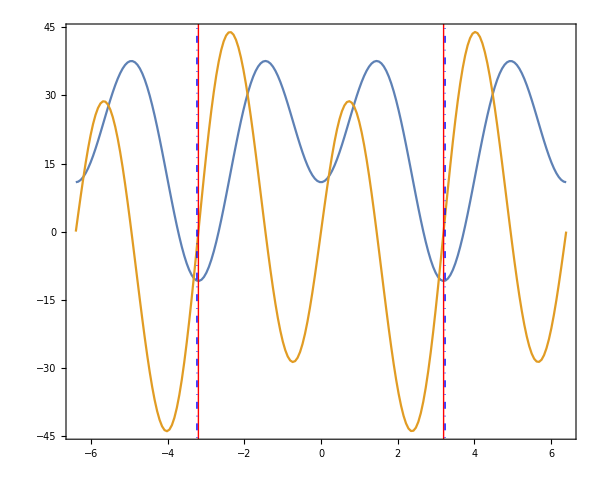

```mathematica
Show[ListLinePlot[{Table[{q,V[q,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]},{q,qvalues[kconst[thetadegfit1]]}],Table[{p,dvdq[p,22.5,kconst[thetadegfit1],thetadegfit1,magicpower]},{p,qvalues[kconst[thetadegfit1]]}]},ImageSize->600,AspectRatio->0.8,Frame->True,Axes->True],Graphics[{Red,Thick,Line[{{-2*period[kconst[thetadegfit1]],-100},{-2*period[kconst[thetadegfit1]],100}}]}],Graphics[{Red,Thick,Line[{{2*period[kconst[thetadegfit1]],-100},{2*period[kconst[thetadegfit1]],100}}]}],Graphics[{Blue,DotDashed,Line[{{-2*period[kconst[thetadegfit1+180]],-100},{-2*period[kconst[thetadegfit1+180]],100}}]}],Graphics[{Blue,DotDashed,Line[{{2*period[kconst[thetadegfit1+180]],-100},{2*period[kconst[thetadegfit1+180]],100}}]}]]
```